```mathematica
csv = Import["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/bounce_solution_beta_45_b_0.25.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
timeframe = Normal@Values@csv[All,"timeframe"];
```

```mathematica
bounce = Normal@Values@csv[All,{"timeframe","bounce"}];
interpolateBounce = Interpolation[bounce];
```

```mathematica
interpolateBounce[0.5]
```

1.12701

```mathematica
coefficients = Import["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/coefficients.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
timeframe = Normal@coefficients[All,"timeframe"];
falseVacuumCoefficient = Normal@Values@coefficients[All,{"timeframe","false_vacuum_coefficient"}];
effectivePotentialCoefficient = Normal@Values@coefficients[All,{"timeframe", "effective_potential_coefficient"}];
```

```mathematica
interpolateFalseVacuumCoefficient = Interpolation[falseVacuumCoefficient];
interpolateEffectivePotentialCoefficient = Interpolation[effectivePotentialCoefficient];
```

```mathematica
vacuumFluctuation[l_,t_]:=1/Sin[t] LegendreP[N[-1/2+I Sqrt[8.5-9/4],MachinePrecision],l+1,N[Cos[t],MachinePrecision]];
```

```mathematica
logarithmicDerivative[l_, t_]=FullSimplify[D[vacuumFluctuation[l, t], t]/vacuumFluctuation[0, t]]
```

(((1.5+2.5 ⅈ) Cos[t] LegendreP[-0.5+2.5 ⅈ,1+l,Cos[t]]+((0.5-2.5 ⅈ)+(1.+2.77556×10^-17 ⅈ) l) LegendreP[0.5+2.5 ⅈ,1+l,Cos[t]]) Sin[t])/((-1.+Cos[t]^2) LegendreP[-0.5+2.5 ⅈ,1,Cos[t]])

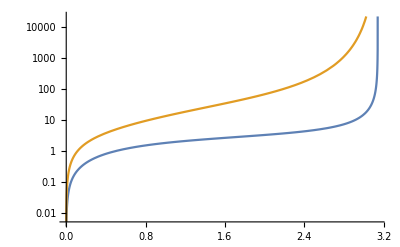

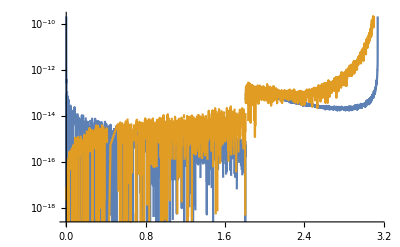

```mathematica
LogPlot[{Re[logarithmicDerivative[0, t]], Re[logarithmicDerivative[2, t]]}, {t, 0, π}]
LogPlot[{Abs[Im[logarithmicDerivative[0, t]]], Abs[Im[logarithmicDerivative[2, t]]]}, {t, 0, π}]
```

```mathematica
zeroFluctuation[π/2]
```

zeroFluctuation[π/2]

```mathematica
coefficients = Import["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/negative_modes_coefficients.csv", "Dataset", "HeaderLines"-> 1];
timeframe = Normal@coefficients[All,"timeframe"];
effectivePotential = Normal@Values@coefficients[All,{"timeframe","effective_potential"}];
interpolateEffectivePotential = Interpolation[effectivePotential, InterpolationOrder->1];
```

```mathematica
interpolateEffectivePotential[0.5]
```

101.112

```mathematica
L = - Φ''[t]- 3 Cot[t] * Φ'[t]  + interpolateEffectivePotential[t] * Φ[t];
NDEigensystem[{L, DirichletCondition[Φ[t]==0,True]},Φ[t],{t,0,π},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}} ]
```

{{-3.52957,62.509,78.3608,83.7337,93.604,100.953,106.729,118.871,132.748,149.245},{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
zeroMode[t_] := InterpolatingFunction[…][t];
```

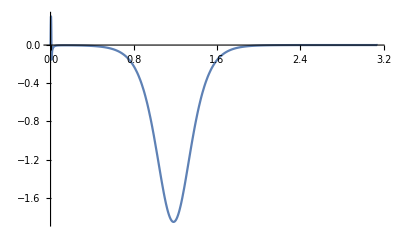

```mathematica
Plot[InterpolatingFunction[…][t], {t, 0, π}]
```

```mathematica
points=Table[{t,zeroMode[t]},{t,0.00001,Pi - 0.00001,π/10000}];
Export["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/negative_mode.csv",points]
```

/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/negative_mode.csv